# Optimal parameter lookup and Limit

## Version 2.00

JSON Import

```mathematica
data = Import[SystemDialogInput["FileOpen"],"RawJSON"];
```

```mathematica
data = Import[SystemDialogInput["FileOpen"],"RawJSON"];
```

```mathematica
Keys[data]
```

{Border,Description,GeometryDifference,Model,RuntimeInfo,Trees,Version}

Visualize and process input JSON

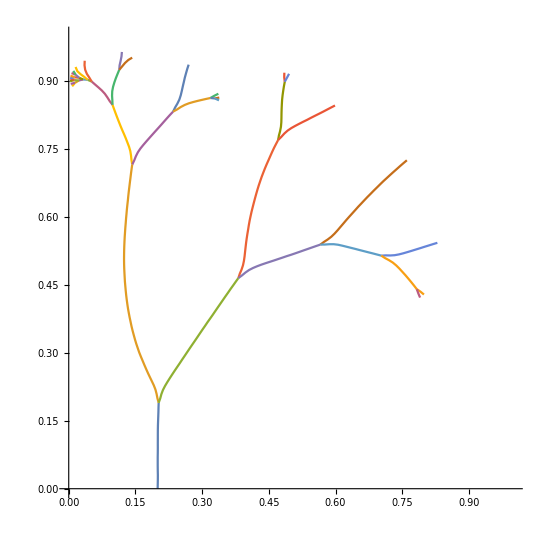

```mathematica
ListPlot[data["Trees"]["Branches"][[All,"coords"]],Joined->True,PlotRange->{{0,1},{0,1}}, AspectRatio->1, Joined->True]
```

### TODO

JSON Export

```mathematica
Options[ModelJSONStructure] = {
"dx"->0.2,
"width"->1,
"height"->1,
"riverBoundaryId"->4,
"boundaryIds"->{1,2,3,4},
"boundaryCondition"->0,
"fieldValue"->1,
"eta"->0,
"biffurcationType"->0,
"biffurcationThreshold"->-0.2,
"biffurcationThreshold2"->0.0001,
"biffurcationAngle"->Pi/10.,
"growthType"->0,
"growthThreshold"->0,
"ds"->0.01,

"integrRadius"->0.03,
"integrExponant"->3,
"weightRadius"->0.02,

"meshEps"->1. 10^-5,
"meshExponant"->3,
"meshRefinmentRadius"->0.06,
"meshMinArea"->1. 10^-8,
"meshMaxArea"->1. 10,
"meshMinAngle"->32,

"quadratureDegree"->3,
"refinmentFraction"->0.05,
"refinmentSteps"->3
};
ModelJSONStructure[OptionsPattern[]]:={
"Model"->{
"width"->OptionValue["width"],
"height"->OptionValue["height"],
"dx"->OptionValue["dx"],
"riverBoundaryId"->OptionValue["riverBoundaryId"],
"boundaryIds"->OptionValue["boundaryIds"],

"boundaryCondition"->OptionValue["boundaryCondition"],
"fieldValue"->OptionValue["fieldValue"],
"eta"->OptionValue["eta"],
"biffurcationType"->OptionValue["biffurcationType"],
"biffurcationThreshold"->OptionValue["biffurcationThreshold"],
"biffurcationThreshold2"->OptionValue["biffurcationThreshold2"],
"biffurcationAngle"->OptionValue["biffurcationAngle"],
"growthType"->OptionValue["growthType"],
"growthThreshold"->OptionValue["growthThreshold"],
"ds"->OptionValue["ds"],

"Mesh"->{
"eps"->OptionValue["meshEps"],
"refinmentRadius"->OptionValue["meshRefinmentRadius"],
"minArea"->OptionValue["meshMinArea"],
"maxArea"->OptionValue["meshMaxArea"],
"minAngle"->OptionValue["meshMinAngle"],
"exponant"->OptionValue["meshExponant"]
},

"Integration"->{
"radius"->OptionValue["integrRadius"],
"weightRadius"->OptionValue["weightRadius"],
"exponant"->OptionValue["integrExponant"]},

"Solver"->{
"quadratureDegree"->OptionValue["quadratureDegree"],
"refinmentFraction"->OptionValue["refinmentFraction"],
"refinmentSteps"->OptionValue["refinmentSteps"]}
}};
```

### Test and example of usage

```mathematica
ModelJSONStructure["dx"->0.19]
```

{Model→{width→1,height→1,dx→0.19,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationAngle→0.314159,growthType→0,growthThreshold→0,ds→0.01,Mesh→{eps→0.00001,refinmentRadius→0.06,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3},Integration→{radius→0.03,exponant→3}}}

```mathematica
Export[NotebookDirectory[]<>"test.json",ModelJSONStructure[]]
```

/home/oleg/dev/riversim/research/test.json

```mathematica
mdl=Import[NotebookDirectory[]<>"test.json"]
```

{Model→{width→1,height→1,dx→0.2,riverBoundaryId→4,boundaryIds→{1,2,3,4},boundaryCondition→0,fieldValue→1,eta→0,biffurcationType→0,biffurcationThreshold→-0.2,biffurcationAngle→0.314159,growthType→0,growthThreshold→0,ds→0.01,Mesh→{eps→0.00001,refinmentRadius→0.06,minArea→1.×10^-8,maxArea→10.,minAngle→32,exponant→3},Integration→{radius→0.03,exponant→3}}}

```mathematica
mdl[[1,1]]
```

Model

Runner

### This function calls riversim program and communicate with it through file

```mathematica
RunSimulation[numOfSteps_:10, modelParams_:ModelJSONStructure[], outputName_:"simdata"]:=Module[{
resultDir="/home/oleg/dev/build",
JSONPath="/home/oleg/dev/build/mdl_data.json",
riversimPath= "/home/oleg/dev/build/source/riversim",
simdataJSONPath = "/home/oleg/dev/build/"<>outputName<>".json"},
Export[
JSONPath,
modelParams
];
RunProcess[{
riversimPath, 
"-o",outputName,
"-n",numOfSteps,
JSONPath},
ProcessDirectory->resultDir
];
Import[simdataJSONPath,"RawJSON"]
];
```

### This is GUI interface for simulation and its data

```mathematica
Manipulate[
ListPlot[
simdata["Trees"]["Branches"][[All,"coords"]],
Joined->True,
PlotRange->{{0,1},{0,1}}, 
AspectRatio->1, 
Joined->True
],

{ds, 0.001, 0.1},
{n,10,150,10},
Button["Run Simulation",
simdata=RunSimulation[n, ModelJSONStructure["ds"->ds]]]
]
```

Run Experiment

```mathematica
resultDir="/home/oleg/dev/build";
JSONPath="/home/oleg/dev/build/input_data.json";
riversimPath= "/home/oleg/dev/build/source/riversim";
outputName = "meshrad_";
```

```mathematica
Module[{ds = 0.01, n = 100, index = 0},
Table[{
(*Exporting simulation parameters*)
Export[
JSONPath,
ModelJSONStructure[
"ds"->ds,
"meshRefinmentRadius"->meshRad]
];
(*Running simmulation*)
log = RunProcess[
{
riversimPath,
"-n",n, 
"-o",outputName <> ToString[meshRad],
JSONPath
},
ProcessDirectory->resultDir
];
(*Printing log*)
log[[-1,-100]]
},
{meshRad, 0.02, 0.4, 0.02}
]];
```

$Aborted

```mathematica
Manipulate[
la,
{η,0,5}]
```

Process Simulation Data

# Dev

```mathematica
z=x
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of x^2.

Hold[z=x]

```mathematica
Button["RunSim",Print[Integrate[x,x]]]
```

RunSim